```mathematica
SetDirectory["/Users/dubard/Documents/Projects/FlexibleNetwork"]
```

/Users/dubard/Documents/Projects/FlexibleNetwork

```mathematica
trainconv = Import["Results/Conv/train_error_rate"];
```

```mathematica
testconv = Import["Results/Conv/test_error_rate"];
```

```mathematica
trainbench = Import["Results/Bench/train_error_rate"][[1;;1000;;4]];
testbench = Import["Results/Bench/test_error_rate"][[1;;1000;;4]];
```

```mathematica
Part
trainbench
```

Part

{{0.,0.293999999999999984},{2.,0.181999999999999995},{4.,0.139000000000000012},{6.,0.1095},{8.,0.102499999999999994},{10.,0.0894999999999999962},{12.,0.0909999999999999976},{14.,0.0859999999999999931},{16.,0.0835000000000000048},{18.,0.0810000000000000026},{20.,0.0785000000000000003},{22.,0.0795000000000000012},{24.,0.0790000000000000008},{26.,0.0785000000000000003},{28.,0.076999999999999999},{30.,0.0739999999999999963},{32.,0.0680000000000000049},{34.,0.0665000000000000036},{36.,0.0685000000000000053},{38.,0.0685000000000000053},{40.,0.0660000000000000031},{42.,0.0609999999999999987},{44.,0.0635000000000000009},{46.,0.0619999999999999996},{48.,0.0599999999999999978},{50.,0.0609999999999999987},{52.,0.0609999999999999987},{54.,0.0630000000000000004},{56.,0.0614999999999999991},{58.,0.0599999999999999978},{60.,0.0589999999999999969},{62.,0.0594999999999999973},{64.,0.0580000000000000029},{66.,0.0565000000000000016},{68.,0.0565000000000000016},{70.,0.0570000000000000021},{72.,0.0560000000000000012},{74.,0.0570000000000000021},{76.,0.0550000000000000003},{78.,0.0560000000000000012},{80.,0.0544999999999999998},{82.,0.0550000000000000003},{84.,0.053499999999999999},{86.,0.0529999999999999985},{88.,0.0509999999999999967},{90.,0.0505000000000000032},{92.,0.0544999999999999998},{94.,0.0524999999999999981},{96.,0.0514999999999999972},{98.,0.0500000000000000028},{100.,0.0495000000000000023},{102.,0.0500000000000000028},{104.,0.0475000000000000006},{106.,0.048000000000000001},{108.,0.048000000000000001},{110.,0.048000000000000001},{112.,0.0459999999999999992},{114.,0.0470000000000000001},{116.,0.0470000000000000001},{118.,0.0454999999999999988},{120.,0.0444999999999999979},{122.,0.043499999999999997},{124.,0.0429999999999999966},{126.,0.0429999999999999966},{128.,0.0429999999999999966},{130.,0.0449999999999999983},{132.,0.0439999999999999975},{134.,0.0429999999999999966},{136.,0.0410000000000000017},{138.,0.0420000000000000026},{140.,0.0420000000000000026},{142.,0.0405000000000000013},{144.,0.0410000000000000017},{146.,0.0405000000000000013},{148.,0.0389999999999999999},{150.,0.0384999999999999995},{152.,0.0384999999999999995},{154.,0.0379999999999999991},{156.,0.0384999999999999995},{158.,0.0374999999999999986},{160.,0.0369999999999999982},{162.,0.0374999999999999986},{164.,0.0374999999999999986},{166.,0.0364999999999999977},{168.,0.0374999999999999986},{170.,0.0359999999999999973},{172.,0.0350000000000000033},{174.,0.0354999999999999968},{176.,0.0369999999999999982},{178.,0.0364999999999999977},{180.,0.0359999999999999973},{182.,0.0354999999999999968},{184.,0.0350000000000000033},{186.,0.0340000000000000024},{188.,0.0340000000000000024},{190.,0.0350000000000000033},{192.,0.0350000000000000033},{194.,0.0345000000000000029},{196.,0.0350000000000000033},{198.,0.0340000000000000024},{200.,0.0325000000000000011},{202.,0.0325000000000000011},{204.,0.0315000000000000002},{206.,0.0309999999999999998},{208.,0.0315000000000000002},{210.,0.0315000000000000002},{212.,0.0309999999999999998},{214.,0.0309999999999999998},{216.,0.0304999999999999993},{218.,0.0315000000000000002},{220.,0.0320000000000000007},{222.,0.0315000000000000002},{224.,0.0309999999999999998},{226.,0.0304999999999999993},{228.,0.0299999999999999989},{230.,0.0299999999999999989},{232.,0.028500000000000001},{234.,0.028500000000000001},{236.,0.0299999999999999989},{238.,0.0294999999999999985},{240.,0.0290000000000000015},{242.,0.028500000000000001},{244.,0.0280000000000000006},{246.,0.028500000000000001},{248.,0.028500000000000001},{250.,0.0264999999999999993},{252.,0.0269999999999999997},{254.,0.0269999999999999997},{256.,0.0269999999999999997},{258.,0.0259999999999999988},{260.,0.0264999999999999993},{262.,0.0269999999999999997},{264.,0.0264999999999999993},{266.,0.0259999999999999988},{268.,0.0264999999999999993},{270.,0.0250000000000000014},{272.,0.0254999999999999984},{274.,0.0259999999999999988},{276.,0.0254999999999999984},{278.,0.0240000000000000005},{280.,0.0240000000000000005},{282.,0.0235000000000000001},{284.,0.0224999999999999992},{286.,0.0235000000000000001},{288.,0.0224999999999999992},{290.,0.0214999999999999983},{292.,0.0210000000000000013},{294.,0.0214999999999999983},{296.,0.0219999999999999987},{298.,0.0214999999999999983},{300.,0.0219999999999999987},{302.,0.0214999999999999983},{304.,0.0214999999999999983},{306.,0.0205000000000000009},{308.,0.0200000000000000004},{310.,0.0179999999999999986},{312.,0.0189999999999999995},{314.,0.0189999999999999995},{316.,0.0165000000000000008},{318.,0.0179999999999999986},{320.,0.0205000000000000009},{322.,0.0214999999999999983},{324.,0.0205000000000000009},{326.,0.0205000000000000009},{328.,0.0200000000000000004},{330.,0.0200000000000000004},{332.,0.0175000000000000017},{334.,0.0170000000000000012},{336.,0.0165000000000000008},{338.,0.0160000000000000003},{340.,0.0149999999999999994},{342.,0.0154999999999999999},{344.,0.0149999999999999994},{346.,0.0149999999999999994},{348.,0.0149999999999999994},{350.,0.0149999999999999994},{352.,0.0160000000000000003},{354.,0.0165000000000000008},{356.,0.0149999999999999994},{358.,0.0154999999999999999},{360.,0.0165000000000000008},{362.,0.0160000000000000003},{364.,0.0145000000000000007},{366.,0.0140000000000000003},{368.,0.0140000000000000003},{370.,0.0145000000000000007},{372.,0.0140000000000000003},{374.,0.0149999999999999994},{376.,0.0145000000000000007},{378.,0.0145000000000000007},{380.,0.0149999999999999994},{382.,0.0149999999999999994},{384.,0.0149999999999999994},{386.,0.0145000000000000007},{388.,0.0140000000000000003},{390.,0.0145000000000000007},{392.,0.0129999999999999994},{394.,0.0114999999999999998},{396.,0.0125000000000000007},{398.,0.0145000000000000007},{400.,0.0140000000000000003},{402.,0.0134999999999999999},{404.,0.0125000000000000007},{406.,0.0109999999999999994},{408.,0.0100000000000000002},{410.,0.0109999999999999994},{412.,0.0109999999999999994},{414.,0.0120000000000000003},{416.,0.0120000000000000003},{418.,0.0114999999999999998},{420.,0.0100000000000000002},{422.,0.00949999999999999976},{424.,0.00949999999999999976},{426.,0.00899999999999999932},{428.,0.00850000000000000061},{430.,0.00949999999999999976},{432.,0.00899999999999999932},{434.,0.00899999999999999932},{436.,0.00800000000000000017},{438.,0.00899999999999999932},{440.,0.00850000000000000061},{442.,0.0100000000000000002},{444.,0.0105000000000000007},{446.,0.00949999999999999976},{448.,0.00850000000000000061},{450.,0.00749999999999999972},{452.,0.00700000000000000015},{454.,0.00949999999999999976},{456.,0.00949999999999999976},{458.,0.0100000000000000002},{460.,0.00899999999999999932},{462.,0.0100000000000000002},{464.,0.00899999999999999932},{466.,0.00800000000000000017},{468.,0.00899999999999999932},{470.,0.00800000000000000017},{472.,0.00600000000000000013},{474.,0.00800000000000000017},{476.,0.00749999999999999972},{478.,0.00600000000000000013},{480.,0.00600000000000000013},{482.,0.00700000000000000015},{484.,0.00749999999999999972},{486.,0.0064999999999999997},{488.,0.00700000000000000015},{490.,0.00400000000000000008},{492.,0.0050000000000000001},{494.,0.00700000000000000015},{496.,0.0064999999999999997},{498.,0.0050000000000000001}}

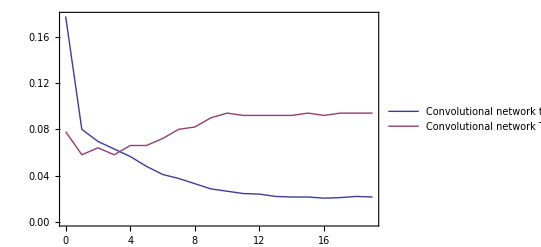

```mathematica
pl = ListLinePlot[{trainconv, testconv }, PlotLegends->{"Convolutional network train error rate", "Convolutional network test error rate"},Frame->True]
```

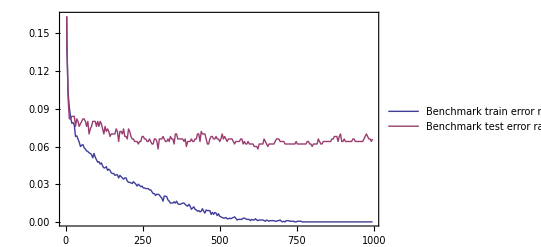

```mathematica
pl2 = ListLinePlot[{trainbench, testbench }, PlotLegends->{"Benchmark train error rate", "Benchmark test error rate"},Frame->True]
```

```mathematica
Export["figs/error_rates_conv.png", pl, ImageResolution->100]
```

```mathematica
"figs/error_rates_conv.png"
Export["figs/error_rates_bench.png", pl2, ImageResolution->100]
```

figs/error_rates_conv.png

figs/error_rates_bench.png

```mathematica
Import["figs/error_rates.png"]
```

-Graphics-